# Manipulate Function

```mathematica
?Manipulate
```

Manipulate[expr,{u,u_min,u_max}] generates a version of expr with controls added to allow interactive manipulation of the value of u. 
Manipulate[expr,{u,u_min,u_max,du}] allows the value of u to vary between u_min and u_max in steps du. 
Manipulate[expr,{{u,u_init},u_min,u_max,…}] takes the initial value of u to be u_init. 
Manipulate[expr,{{u,u_init,u_lbl},…}] labels the controls for u with u_lbl. 
Manipulate[expr,{u,{u_1,u_2,…}}] allows u to take on discrete values u_1,u_2,…. 
Manipulate[expr,{u,…},{v,…},…] provides controls to manipulate each of the u,v,…. 
Manipulate[expr,c_u→{u,…},c_v→{v,…},…] links the controls to the specified controllers on an external device.

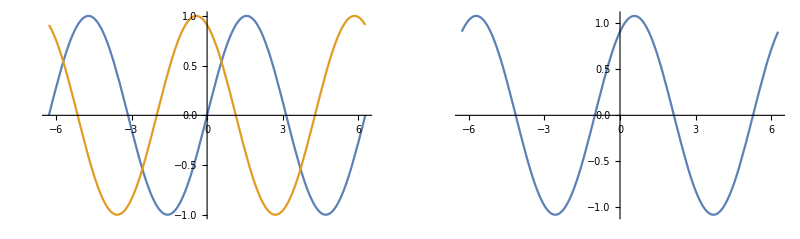

```mathematica
GraphicsRow[{
Plot[{Sin[x], Sin[x+2]}, {x, -2Pi, 2Pi}],
Plot[Sin[x]+Sin[x+2], {x, -2Pi, 2Pi}]
}, ImageSize->Full]
```

```mathematica
Manipulate[
GraphicsRow[{
Plot[{Sin[x], Sin[x+phi]}, {x, -2Pi, 2Pi}, PlotRange->{Automatic, {-2, 2}}],
Plot[Sin[x]+Sin[x+phi], {x, -2Pi, 2Pi}, PlotRange->{Automatic, {-2, 2}}]
}, ImageSize->Full],
{phi, 0, 2Pi}]
```

```mathematica
Manipulate[
Plot[A Sin[w t + ϕ], {t, -2Pi, 2Pi}, PlotRange->{Automatic, {-2, 2}}, ImageSize->Full],
{{A, 0.5, "Amplitude"}, 0, 2},
{{w, 1,      "Frequency"}, 0, 10},
{{ϕ, 0,   "Phase Shift"}, 0, 2Pi}
]
```

```mathematica
Manipulate[
Plot[A lambda[w t + ϕ], {t, -2Pi, 2Pi}, PlotRange->{Automatic, {-2, 2}}, ImageSize->Full],
{{A, 0.5, "Amplitude"}, 0, 2},
{{w, 1,      "Frequency"}, 0, 10},
{{ϕ, 0,   "Phase Shift"}, 0, 2Pi},
{{lambda, Sin, "Function"}, {Sin, Cos, Tan, Cot}}
]
```